# MathIOmica: Dynamic Transcriptome

Loading the MathIOmica Packagepaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#2133290847 | Classification, Clustering  and Visualization of Transcriptome Time Seriespaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#834625544
Importing OmicsObject Transcriptome Datapaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#257268298 | Annotation and Enrichmentpaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#2035743524
Processing OmicsObject Transcriptome Datapaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#208227830 | Appendix: All Commands Up to Enrichment Analysis in One Steppaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#981111770
Resampling Transcriptome Datapaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#1956292219 |

The MathIOmica Dynamic Transcriptome is a brief guide to analyzing the dynamics of transcriptome data. The presentation is streamlined, without discussion of the functions used, but with links to each function provided at each step of the calculation. For more details consult MathIOmica's documentation of each funciton, and the MathIOmica Tutorial for a deeper presentation of a multiple omics analysis.

## Loading the MathIOmica Package

The functions defined in the MathIOmica` context provide support for conducting analyses of omics data (See also the MathIOmica Overview).

This loads the package:

```mathematica
<<MathIOmica`
```

## Importing OmicsObject Transcriptome Data

We first import the transcriptomics data example (for details on how to import such data please refer to DataImporterpaclet:MathIOmica/ref/DataImporter, DataImporterDirectpaclet:MathIOmica/ref/DataImporterDirect, DataImporterDirectLabeledpaclet:MathIOmica/ref/DataImporterDirectLabeled and OmicsObjectCreatorpaclet:MathIOmica/ref/OmicsObjectCreator documentation).

We import the transcriptomics OmicsObject

```mathematica
rnaExample=Get[FileNameJoin[{ConstantMathIOmicaExamplesDirectory,"rnaExample"}]]
```

<|7→<|{FAM138A,RNA}→{{0},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{2.73998},{OK}},25262,{LOC100507412,RNA}→{{0},{OK}},{RNA45S5,RNA}→{{0},{OK}},{DUX4L,RNA}→{{0},{OK}}|>,8→<|1|>,11,20→1,21→<|1|>|>
 |  |  |  |

There are multiple samples given by the outer associations. We can use Query to get any data. For example we can get the outer keys:

```mathematica
Query[Keys]@rnaExample
```

{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

We form an association between samples to actual days of the study:

```mathematica
sampleToDays= <|"7"->"186","8"->"255","9"->"289","10"->"290","11"->"292","12"->"294","13"->"297","14"->"301","15"->"307","16"->"311","17"->"322","18"->"329","19"->"369","20"->"380","21"->"400"|>;
```

We can now do a KeyMap to rename the outer keys:

```mathematica
rnaLongitudinal=KeyMap[sampleToDays,rnaExample]
```

<|186→<|{FAM138A,RNA}→{{0},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{2.73998},{OK}},25262,{LOC100507412,RNA}→{{0},{OK}},{RNA45S5,RNA}→{{0},{OK}},{DUX4L,RNA}→{{0},{OK}}|>,255→<|1|>,11,380→1,400→<|1|>|>
 |  |  |  |

## Processing OmicsObject Transcriptome Data

We normalize the transcriptome data using the QuantileNormalizationpaclet:MathIOmica/ref/QuantileNormalization function.

```mathematica
rnaQuantileNormed=QuantileNormalization[rnaLongitudinal,ListIndex-> 1,ComponentIndex-> 1]
```

<|186→<|{FAM138A,RNA}→{{0.},{OK}},{OR4F5,RNA}→{{0.},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25262,{LOC100507412,RNA}→{{0.},{OK}},{RNA45S5,RNA}→{{0.},{OK}},{DUX4L,RNA}→{{0.},{OK}}|>,13,400→<|1|>|>
 |  |  |  |

We first use  LowValueTagpaclet:MathIOmica/ref/LowValueTag to tag values of 0 as Missing[]:

```mathematica
rnaZeroTagged=LowValueTag[rnaQuantileNormed,0]
```

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25263,{RNA45S5,RNA}→{{Missing[]},{OK}},{DUX4L,RNA}→{{Missing[]},{OK}}|>,255→<|1|>,11,1,400→<|1|>|>
 |  |  |  |

We next use  LowValueTagpaclet:MathIOmica/ref/LowValueTag again to set all FPKM values <1 to unity:

```mathematica
rnaNoiseAdjusted=LowValueTag[rnaZeroTagged,1,ValueReplacement-> 1]
```

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25263,{RNA45S5,RNA}→{{Missing[]},{OK}},{DUX4L,RNA}→{{Missing[]},{OK}}|>,255→<|1|>,11,1,400→<|1|>|>
 |  |  |  |

We filter out data  using FilterMissingpaclet:MathIOmica/ref/FilterMissing where the reference healthy point "255" is missing and retain data with at least 3/4 points available:

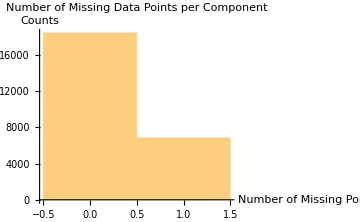

{Missing -> Counts: ,<|0→18427,1→6841|>}

-Graphics-

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25263,{RNA45S5,RNA}→{{Missing[]},{OK}},{DUX4L,RNA}→{{Missing[]},{OK}}|>,255→<|1|>,11,1,400→<|1|>|>
 |  |  |  |

```mathematica
rnaFiltered=FilterMissing[rnaNoiseAdjusted,3/4,Reference-> "255"]
```

We extract the times for the filtered RNA data using TimeExtractorpaclet:MathIOmica/ref/TimeExtractor:

```mathematica
timesRNA=TimeExtractor[rnaFiltered]
```

{186,255,289,290,292,294,297,301,307,311,322,329,369,380,400}

For each gene we now extract a time series (list of values) corresponding to these times using CreateTimeSeriespaclet:MathIOmica/ref/CreateTimeSeries:

```mathematica
timeSeriesRNA=CreateTimeSeries[rnaFiltered]
```

<|{FAM138A,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{OR4F5,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{LOC729737,RNA}→{2.2946,1,4.67694,4.48131,4.95507,1,1.25726,2.14767,1.93219,1,2.58217,2.31301,4.10284,3.80929,1.45471},{DDX11L1,RNA}→{5.91665,4.32081,3.19599,3.64164,2.7327,2.13461,2.17168,3.23429,1.89576,3.0267,4.34004,7.27001,2.01132,9.27701,7.54415},25260,{RNA5-8S5,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{LOC100507412,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{RNA45S5,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{DUX4L,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>
 |  |  |  |

We use SeriesApplierpaclet:MathIOmica/ref/SeriesApplier to implement a logarithm transformation:

```mathematica
timeSeriesRNALog=SeriesApplier[Log,timeSeriesRNA]
```

<|{FAM138A,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{OR4F5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{0.830556,0,1.54264,1.49992,1.60041,0,0.228935,0.764385,0.658653,0,0.94863,0.838548,1.41168,1.33744,0.374807},{DDX11L1,RNA}→{1.77777,1.46344,1.1619,1.29243,1.00529,0.758282,0.775501,1.17381,0.639619,1.10747,1.46788,1.98376,0.698792,2.22754,2.02077},25260,{RNA5-8S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC100507412,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{RNA45S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{DUX4L,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>
 |  |  |  |

We compare every value in each series to the healthy "255" time point, which is the second element in each series. We use SeriesInternalComparepaclet:MathIOmica/ref/SeriesInternalCompare:

```mathematica
rnaCompared=SeriesInternalCompare[timeSeriesRNALog,ComparisonIndex->2]
```

<|{FAM138A,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{OR4F5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{0.830556,0,1.54264,1.49992,1.60041,0,0.228935,0.764385,0.658653,0,0.94863,0.838548,1.41168,1.33744,0.374807},{DDX11L1,RNA}→{0.314326,0.,-0.301545,-0.171011,-0.458154,-0.705162,-0.687943,-0.289634,-0.823824,-0.35597,0.00444068,0.520314,-0.764652,0.764095,0.557328},25260,{RNA5-8S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC100507412,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{RNA45S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{DUX4L,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>
 |  |  |  |

Next, we normalize each series, using again SeriesApplierpaclet:MathIOmica/ref/SeriesApplier:

```mathematica
normedRNACompared=SeriesApplier[Normalize,rnaCompared]
```

<|{FAM138A,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{OR4F5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{0.218293,0.,0.40545,0.39422,0.420632,0.,0.0601705,0.200902,0.173112,0.,0.249326,0.220394,0.371029,0.351517,0.0985097},{DDX11L1,RNA}→{0.156411,0.,-0.150051,-0.0850959,-0.22798,-0.350893,-0.342324,-0.144124,-0.40994,-0.177133,0.00220971,0.258911,-0.380495,0.380218,0.27733},25260,{RNA5-8S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC100507412,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{RNA45S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{DUX4L,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>
 |  |  |  |

Finally, we use ConstantSeriesCleanpaclet:MathIOmica/ref/ConstantSeriesClean to remove constant series, as we are interested in changing time patterns:

```mathematica
rnaFinalTimeSeries=ConstantSeriesClean[normedRNACompared]
```

Removed series and returning filtered list. If you would like a list of removed keys run the command ConstantSeriesClean[data,ReturnDropped → True].

<|{LOC729737,RNA}→{0.218293,0.,0.40545,0.39422,0.420632,0.,0.0601705,0.200902,0.173112,0.,0.249326,0.220394,0.371029,0.351517,0.0985097},11782,{UTY,RNA}→{-0.0324671,0.,-0.0127666,-0.256982,-0.0805343,-0.152071,3,-0.198929,-0.280753,-0.310545,-0.339742,-0.346361,-0.542312}|>
 |  |  |  |

## Resampling Transcriptome Data

In addition to the above, we want to create a resampled distribution for the transcriptome dataset prior to classification and clustering.  We repeat the steps in the processing section above using a resampled set of measurements.

We create a resampling of 100000 sets using  BootstrapGeneralpaclet:MathIOmica/ref/BootstrapGeneral:

```mathematica
rnaBootstrap=BootstrapGeneral[rnaLongitudinal,100000]
```

<|186→<|1→{{0},{OK}},2→{{0},{OK}},3→{{10.0429},{OK}},4→{{12.8612},{OK}},5→{{2.37963},{OK}},99991,99997→{{43.8242},{OK}},99998→{{2.40797},{OK}},99999→{{4.68299},{OK}},100000→{{3.29531},{OK}}|>,255→<|1|>,11,1,400→<|1|>|>
 |  |  |  |

As with the regular data we: 1. normalize , 2. tag zero values, 3. tag values of FPKM <1, 4. filter missing data, 5. create a time series, 6. take a logarithm, 7. compare to "255" reference, 8. take the norm of each time series, 9. clean out constant series

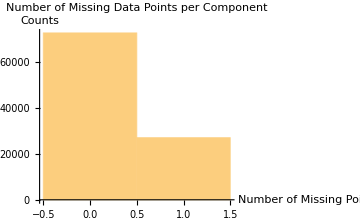

{Missing -> Counts: ,<|0→72867,1→27133|>}

-Graphics-

Removed series and returning filtered list. If you would like a list of removed keys run the command ConstantSeriesClean[data,ReturnDropped → True].

```mathematica
(*1*)rnaBootstrapQuantileNormed=QuantileNormalization[rnaBootstrap,ListIndex-> 1,ComponentIndex-> 1];
(*2*)rnaBootstrapZeroTagged=LowValueTag[rnaBootstrapQuantileNormed,0];
(*3*) rnaBootstrapNoiseAdjusted=LowValueTag[rnaBootstrapZeroTagged,1,ValueReplacement-> 1];
(*4*) rnaBootstrapFiltered=FilterMissing[rnaBootstrapNoiseAdjusted,3/4,Reference-> "255"];
(*5*) timeSeriesBootstrapRNA=CreateTimeSeries[rnaBootstrapFiltered];
(*6*) timeSeriesBootstrapRNALog=SeriesApplier[Log,timeSeriesBootstrapRNA];
(*7*)rnaBootstrapCompared=SeriesInternalCompare[timeSeriesBootstrapRNALog,ComparisonIndex->2];
(*8*)normedBootstrapRNACompared=SeriesApplier[Normalize,rnaBootstrapCompared];
(*9*)rnaBootstrapFinalTimeSeries=ConstantSeriesClean[normedBootstrapRNACompared];
```

## Classification, Clustering and Visualization of Transcriptome Time Series

In this section we will classify the transcriptome time series based on patterns in the series. For the classification we will use TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification.

Before we classify our transcriptome data, we estimate for the "LombScargle" Method a 0.95 quantile cutoff from the bootstrap transcriptome data using QuantileEstimatorpaclet:MathIOmica/ref/QuantileEstimator:

```mathematica
q95RNA=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA]
```

0.85987

Next, we estimate the "Spikes" 0.95 quantile cutoff from the bootstrap transcriptome data:

```mathematica
q95RNASpikes=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA,Method-> "Spikes"]
```

<|14→{0.886757,-0.348387},15→{0.861302,-0.337344}|>

Now we can classify the transcriptome time series data based on these cutoffs using TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification:

```mathematica
rnaClassification=TimeSeriesClassification[rnaFinalTimeSeries,timesRNA,LombScargleCutoff-> q95RNA,SpikeCutoffs->q95RNASpikes]
```

Method → "LombScargle"

<|SpikeMax→<|1|>,7,f7→<|{MIR6723,RNA}→{{0.214503,0.000338299,0.0390479,0.0653206,0.291434,0.336712,0.865961},{1}},60,{DNASE1L1,RNA}→1|>|>
 |  |  |  |

To obtain the possible frequencies we simply run LombScarglepaclet:MathIOmica/ref/LombScargle over the desired times for one of the time series and set the FrequenciesOnly option to Truepaclet:ref/True:

```mathematica
LombScargle[rnaFinalTimeSeries[[1]],timesRNA,FrequenciesOnly-> True]
```

<|f1→0.00500668,f2→0.0104306,f3→0.0158545,f4→0.0212784,f5→0.0267023,f6→0.0321262,f7→0.0375501|>

We now cluster our RNA data using TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters:

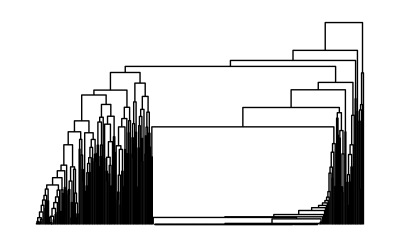
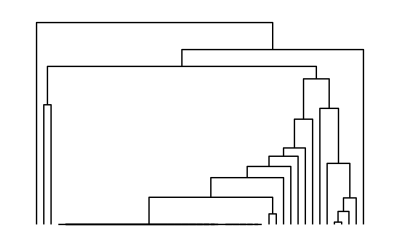
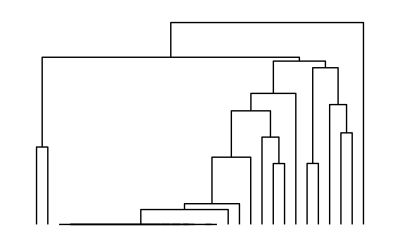
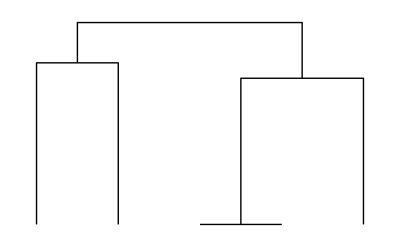
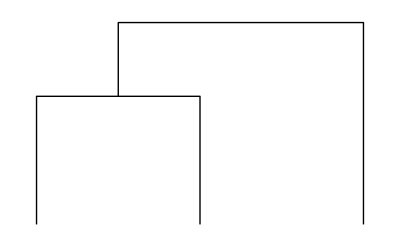
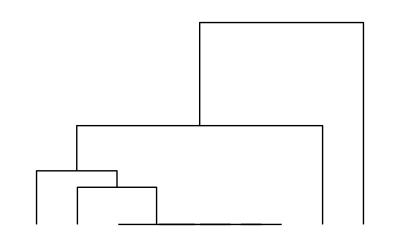
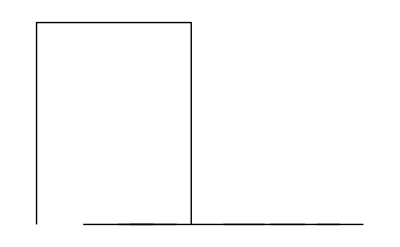
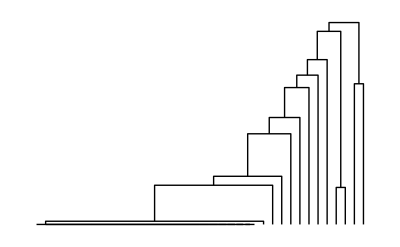
<|SpikeMax→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-,{G1S3}→-Graphics-,{G1S4}→-Graphics-,{G1S5}→-Graphics-,{G1S6}→-Graphics-,{G1S7}→-Graphics-,{G1S8}→-Graphics-,{G1S9}→-Graphics-,{G1S10}→-Graphics-,{G1S11}→-Graphics-,{G1S12}→-Graphics-,{G1S13}→-Graphics-,{G1S14}→-Graphics-|>|>,SpikeMin→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-,{G1S3}→-Graphics-|>|>,f1→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>|>,f2→<|G1→<|{G1S1}→-Graphics-|>,G2→<|{G2S1}→{{0.283264,0.,0.149932,0.415971,0.146512,0.2947,0.267954,0.15466,0.432236,0.281295,0.151677,0.170078,0.149432,0.249221,0.343349}→{POMP,RNA}}|>|>,f3→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>,G2→<|{G2S1}→{{-0.0325957,0.,0.295712,0.400274,0.29765,0.246613,0.0892792,0.27966,0.493911,0.0203708,0.100827,0.223014,0.386987,0.111948,0.221638}→{DUSP23,RNA}},{G2S2}→-Graphics-|>,G3→<|{G3S1}→-Graphics-,{G3S2}→{{-0.0555808,0.,0.317043,0.41872,0.395921,0.283783,0.184223,0.30154,0.265713,0.167588,0.138036,0.110511,0.434502,0.0277974,0.198492}→{PYCARD,RNA}}|>,G4→<|{G4S1}→-Graphics-,{G4S2}→{{0.0572204,0.,-0.22398,-0.11871,-0.0686182,-0.0820599,-0.216559,-0.187636,-0.682766,0.0415532,-0.197678,0.14124,-0.497177,-0.0370276,0.251877}→{ST7,RNA}}|>|>,f4→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>,G2→<|{G2S1}→-Graphics-,{G2S2}→-Graphics-|>|>,f5→<|G1→<|{G1S1}→{{-0.335157,0.,0.107286,0.337104,-0.0121183,0.243878,0.043649,-0.0358548,0.410512,0.305297,0.354136,0.00802356,0.0854209,0.461454,0.303753}→{ALG14,RNA}},{G1S2}→-Graphics-,{G1S3}→-Graphics-|>,G2→<|{G2S1}→-Graphics-,{G2S2}→-Graphics-,{G2S3}→-Graphics-|>|>,f6→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>,G2→<|{G2S1}→-Graphics-,{G2S2}→-Graphics-|>|>,f7→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>,G2→<|{G2S1}→-Graphics-,{G2S2}→-Graphics-,{G2S3}→-Graphics-|>|>|>

<|1|>
 |  |  |  |

```mathematica
rnaClusters=TimeSeriesClusters[rnaClassification, PrintDendrograms-> True]
```

For each class we can generate a dendrogram/heatmap plot using TimeSeriesDendrogramsHeatmapspaclet:MathIOmica/ref/TimeSeriesDendrogramsHeatmaps, with groupings represented on the left, and highlighted to represent the grouping level. The G, S, columns represent the groupings and subgroupings generated by the clustering.  The legend shows the corresponding groupings and subgrouping, and the number of elements in each group subgroup.

```mathematica
TimeSeriesDendrogramsHeatmaps[rnaClusters]
```

-Graphics-

## Annotation and Enrichment

We can carry out Gene Ontology analysis using GOAnalysispaclet:MathIOmica/ref/GOAnalysis for all the classes and groups/subgroups. We only report terms for which there are at least 3 members (2 sets of GO terms, one each for proteomics and transcriptomics).  Please note that this may be a time consuming computation.

```mathematica
goAnalysisRNA=GOAnalysis[rnaClusters,OntologyLengthFilter-> 3,ReportFilter-> 3 ];
```

The output of GOAnalysispaclet:MathIOmica/ref/GOAnalysis has enrichments for each class and group

```mathematica
Query[Keys]@goAnalysisRNA
```

{SpikeMax,SpikeMin,f1,f2,f3,f4,f5,f6,f7}

```mathematica
Query[All,Keys]@goAnalysisRNA
```

<|SpikeMax→{G1S1,G1S2,G1S3,G1S4,G1S5,G1S6,G1S7,G1S8,G1S9,G1S10,G1S11,G1S12,G1S13,G1S14},SpikeMin→{G1S1,G1S2,G1S3},f1→{G1S1,G1S2},f2→{G1S1,G2S1},f3→{G1S1,G1S2,G2S1,G2S2,G3S1,G3S2,G4S1,G4S2},f4→{G1S1,G1S2,G2S1,G2S2},f5→{G1S1,G1S2,G1S3,G2S1,G2S2,G2S3},f6→{G1S1,G1S2,G2S1,G2S2},f7→{G1S1,G1S2,G2S1,G2S2,G2S3}|>

We can view results for any of the groups (and also check out the behavior using the heatmaps generated in the previous section

```mathematica
Query["SpikeMax","G1S1"]@goAnalysisRNA
```

<|GO:0005515→{{1.22292×10^-16,1.40636×10^-13,True},{193,8801,47241,86},{{protein binding,molecular_function},{{{AHI1,RNA}},{{FAM153C,RNA}},{{SASS6,RNA}},{{AP1S3,RNA}},{{ERO1LB,RNA}},{{ABL2,RNA}},{{KIAA0020,RNA}},{{EPM2AIP1,RNA}},{{TUBGCP4,RNA}},{{SNTB2,RNA}},{{SRRM1,RNA}},{{PIAS2,RNA}},{{CUL5,RNA}},{{CEP135,RNA}},{{RAD50,RNA}},{{USP8,RNA}},{{RB1CC1,RNA}},{{NEK1,RNA}},{{KPNA5,RNA}},{{PWWP2A,RNA}},{{ARL13B,RNA}},{{STRN3,RNA}},{{CHD9,RNA}},{{PAG1,RNA}},{{RAB3IP,RNA}},{{TAOK3,RNA}},{{TLK2,RNA}},{{PRPF4B,RNA}},{{TRIP11,RNA}},{{MLLT4,RNA}},{{HELLS,RNA}},{{ITSN1,RNA}},{{SPRY1,RNA}},{{PSMD11,RNA}},{{AZI2,RNA}},{{SYNJ2BP,RNA}},{{RAB11FIP2,RNA}},{{ZFHX3,RNA}},{{SLC4A1AP,RNA}},{{PLCB1,RNA}},{{UGGT1,RNA}},{{ATXN2,RNA}},{{LCOR,RNA}},{{KLHL42,RNA}},{{ITSN2,RNA}},{{CD84,RNA}},{{LGALS8,RNA}},{{HMBOX1,RNA}},{{KIF3B,RNA}},{{EEA1,RNA}},{{DCUN1D5,RNA}},{{NEGR1,RNA}},{{LYSMD1,RNA}},{{PPP1R12B,RNA}},{{KIAA1377,RNA}},{{CCDC153,RNA}},{{PDE1B,RNA}},{{CEP152,RNA}},{{SLC24A1,RNA}},{{BRCA1,RNA}},{{KIAA1683,RNA}},{{DNAJC27,RNA}},{{MAP4K3,RNA}},{{ICA1L,RNA}},{{BARD1,RNA}},{{KIAA1524,RNA}},{{CXCL2,RNA}},{{SMAD1,RNA}},{{HOMER1,RNA}},{{CCDC170,RNA}},{{CCDC146,RNA}},{{RFX3,RNA}},{{ZNF169,RNA}},{{SCAI,RNA}},{{CPEB3,RNA}},{{CCL4L2,RNA}},{{SGOL2,RNA}},{{ALS2CR12,RNA}},{{JAKMIP2,RNA}},{{HCST,RNA}},{{NTNG2,RNA}},{{PRKCDBP,RNA}},{{HES1,RNA}},{{EVI5,RNA}},{{INSR,RNA}},{{ZFC3H1,RNA}}}}},GO:0005737→{{3.78446×10^-10,2.17606×10^-7,True},{193,6648,47241,61},{{cytoplasm,cellular_component},{{{GDPD1,RNA}},{{KIAA1731,RNA}},{{AK9,RNA}},{{DGKE,RNA}},{{CELF2,RNA}},{{NAPEPLD,RNA}},{{TYW5,RNA}},{{LPIN1,RNA}},{{EPM2AIP1,RNA}},{{SNTB2,RNA}},{{BDP1,RNA}},{{USP8,RNA}},{{RB1CC1,RNA}},{{NEK1,RNA}},{{KPNA5,RNA}},{{STRN3,RNA}},{{CHD9,RNA}},{{TAOK3,RNA}},{{MLLT4,RNA}},{{BGLAP,RNA}},{{PRR11,RNA}},{{SPATS2L,RNA}},{{SPRY1,RNA}},{{AZI2,RNA}},{{MAP7D3,RNA}},{{ZFHX3,RNA}},{{SLC4A1AP,RNA}},{{PLCB1,RNA}},{{DHX33,RNA}},{{ATXN2,RNA}},{{KLHL42,RNA}},{{ITSN2,RNA}},{{HMBOX1,RNA}},{{EEA1,RNA}},{{PPIAL4D,RNA},{PPIAL4E,RNA}},{{AS3MT,RNA}},{{HRASLS2,RNA}},{{KIAA1377,RNA}},{{FGD6,RNA}},{{ANKS1B,RNA}},{{CEP128,RNA}},{{BRCA1,RNA}},{{RNF165,RNA}},{{MAP4K3,RNA}},{{BARD1,RNA}},{{KIAA1524,RNA}},{{GK5,RNA}},{{SPATA5,RNA}},{{CCRN4L,RNA}},{{SMAD1,RNA}},{{GDAP1,RNA}},{{SCAI,RNA}},{{CPEB3,RNA}},{{RNASEK-C17orf49,RNA}},{{ALS2CR12,RNA}},{{NME9,RNA}},{{HSP90AB4P,RNA}},{{CNTLN,RNA}},{{PRKCDBP,RNA}},{{HES1,RNA}},{{SAPCD2,RNA}}}}},GO:0005814→{{2.31616×10^-9,8.1084×10^-7,True},{193,123,47241,9},{{centriole,cellular_component},{{{AHI1,RNA}},{{KIAA1731,RNA}},{{SASS6,RNA}},{{CEP135,RNA}},{{SCLT1,RNA}},{{CEP128,RNA}},{{CEP152,RNA}},{{CCDC146,RNA}},{{CNTLN,RNA}}}}},GO:0005813→{{2.82031×10^-9,8.1084×10^-7,True},{193,581,47241,16},{{centrosome,cellular_component},{{{AHI1,RNA}},{{KIAA1731,RNA}},{{SASS6,RNA}},{{ANKRD26,RNA}},{{TUBGCP4,RNA}},{{CEP135,RNA}},{{NEK1,RNA}},{{RAB3IP,RNA}},{{SCLT1,RNA}},{{MAP7D3,RNA}},{{ITSN2,RNA}},{{KIF3B,RNA}},{{KIAA1377,RNA}},{{CCDC15,RNA}},{{IKZF4,RNA}},{{CEP152,RNA}}}}},GO:0005634→{{8.50629×10^-9,1.95645×10^-6,True},{193,7197,47241,61},{{nucleus,cellular_component},{{{AK9,RNA}},{{ZNF286B,RNA}},{{CELF2,RNA}},{{ZFP14,RNA}},{{LPIN1,RNA}},{{SRRM1,RNA}},{{PIAS2,RNA}},{{NEK1,RNA}},{{STRN3,RNA}},{{CHD9,RNA}},{{ZNF292,RNA}},{{RAB3IP,RNA}},{{TLK2,RNA}},{{TRIP11,RNA}},{{HELLS,RNA}},{{PRR11,RNA}},{{PSMD11,RNA}},{{MAP7D3,RNA}},{{DHX29,RNA}},{{ZFHX3,RNA}},{{SLC4A1AP,RNA}},{{MITF,RNA}},{{PLCB1,RNA}},{{LCOR,RNA}},{{HELZ,RNA}},{{HMBOX1,RNA}},{{SP110,RNA}},{{NFIA,RNA}},{{IKZF4,RNA}},{{ZNF605,RNA}},{{BRCA1,RNA}},{{RNF165,RNA}},{{ZNF763,RNA}},{{KIAA1683,RNA}},{{ZNF682,RNA}},{{ZNF829,RNA}},{{DNAJC27,RNA}},{{BARD1,RNA}},{{SYCP2,RNA}},{{CCRN4L,RNA}},{{SMAD1,RNA}},{{PPARGC1B,RNA}},{{SUMO4,RNA}},{{GDAP1,RNA}},{{RFX3,RNA}},{{ZNF169,RNA}},{{FKTN,RNA}},{{SCAI,RNA}},{{RPA4,RNA}},{{CPEB3,RNA}},{{ZNF563,RNA}},{{ZNF573,RNA}},{{ZNF618,RNA}},{{ZNF514,RNA}},{{UBN2,RNA}},{{HES1,RNA}},{{ZNF503,RNA}},{{SAPCD2,RNA}},{{EVI5,RNA}},{{INSR,RNA}},{{USP36,RNA}}}}},GO:0005654→{{5.3418×10^-8,0.0000102384,True},{193,3749,47241,39},{{nucleoplasm,cellular_component},{{{AK9,RNA}},{{LPIN1,RNA}},{{KIAA0020,RNA}},{{EPM2AIP1,RNA}},{{SRRM1,RNA}},{{CHD6,RNA}},{{BDP1,RNA}},{{PIAS2,RNA}},{{RAD50,RNA}},{{USP8,RNA}},{{KPNA5,RNA}},{{STRN3,RNA}},{{CHD9,RNA}},{{PRPF4B,RNA}},{{MLLT4,RNA}},{{SPRY1,RNA}},{{PSMD11,RNA}},{{MAP7D3,RNA}},{{RAB11FIP2,RNA}},{{ZFHX3,RNA}},{{SLC4A1AP,RNA}},{{DHX33,RNA}},{{ATXN2,RNA}},{{NFIA,RNA}},{{PPP1R12B,RNA}},{{IKZF4,RNA}},{{CEP152,RNA}},{{BRCA1,RNA}},{{BARD1,RNA}},{{CCRN4L,RNA}},{{SMAD1,RNA}},{{PPARGC1B,RNA}},{{C8orf44,RNA}},{{SCAI,RNA}},{{RPA4,RNA}},{{RNASEK-C17orf49,RNA}},{{SGOL2,RNA}},{{UBN2,RNA}},{{HES1,RNA}}}}},GO:0042384→{{2.50214×10^-7,0.0000411066,True},{193,153,47241,8},{{cilium assembly,biological_process},{{{AHI1,RNA}},{{NEK1,RNA}},{{ARL13B,RNA}},{{RAB3IP,RNA}},{{SCLT1,RNA}},{{KIAA1377,RNA}},{{RFX3,RNA}},{{WDPCP,RNA}}}}},GO:0003677→{{3.68453×10^-7,0.000052965,True},{193,2344,47241,28},{{DNA binding,molecular_function},{{{ZNF286B,RNA}},{{ZFP14,RNA}},{{KIAA0020,RNA}},{{EPM2AIP1,RNA}},{{SRRM1,RNA}},{{CHD6,RNA}},{{BDP1,RNA}},{{PIAS2,RNA}},{{RAD50,RNA}},{{CHD9,RNA}},{{ZNF292,RNA}},{{LCOR,RNA}},{{HMBOX1,RNA}},{{SP110,RNA}},{{ZNF605,RNA}},{{BRCA1,RNA}},{{ZNF763,RNA}},{{ZNF829,RNA}},{{SYCP2,RNA}},{{ZBED3,RNA}},{{RFX3,RNA}},{{ZNF169,RNA}},{{RNASEK-C17orf49,RNA}},{{ZNF563,RNA}},{{ZNF573,RNA}},{{ZNF618,RNA}},{{ZNF514,RNA}},{{HES1,RNA}}}}},GO:0005829→{{1.78908×10^-6,0.000228605,True},{193,3476,47241,34},{{cytosol,cellular_component},{{{AHI1,RNA}},{{AK9,RNA}},{{AP1S3,RNA}},{{ABL2,RNA}},{{LPIN1,RNA}},{{TUBGCP4,RNA}},{{SRRM1,RNA}},{{CUL5,RNA}},{{CEP135,RNA}},{{USP8,RNA}},{{RB1CC1,RNA}},{{KPNA5,RNA}},{{RAB3IP,RNA}},{{MLLT4,RNA}},{{ITSN1,RNA}},{{SPRY1,RNA}},{{PSMD11,RNA}},{{SCLT1,RNA}},{{PLCB1,RNA}},{{LGALS8,RNA}},{{KIF3B,RNA}},{{EEA1,RNA}},{{PPP1R12B,RNA}},{{AS3MT,RNA}},{{PDE1B,RNA}},{{ARHGAP11B,RNA}},{{CEP152,RNA}},{{SMAD1,RNA}},{{ZBED3,RNA}},{{SGOL2,RNA}},{{EVI5,RNA}},{{INSR,RNA}},{{UTS2,RNA}},{{ATG10,RNA}}}}},GO:0006351→{{2.45157×10^-6,0.000281931,True},{193,2285,47241,26},{{transcription, DNA-templated,biological_process},{{{ZNF286B,RNA}},{{ZFP14,RNA}},{{LPIN1,RNA}},{{CHD6,RNA}},{{BDP1,RNA}},{{PIAS2,RNA}},{{RB1CC1,RNA}},{{CHD9,RNA}},{{HELLS,RNA}},{{HMBOX1,RNA}},{{SP110,RNA}},{{IKZF4,RNA}},{{ZNF605,RNA}},{{BRCA1,RNA}},{{ZNF763,RNA}},{{ZNF682,RNA}},{{ZNF829,RNA}},{{RFX3,RNA}},{{ZNF169,RNA}},{{SCAI,RNA}},{{ZNF563,RNA}},{{ZNF573,RNA}},{{ZNF618,RNA}},{{ZNF514,RNA}},{{HES1,RNA}},{{ZNF503,RNA}}}}},GO:0043234→{{0.0000174221,0.0018214,True},{193,355,47241,9},{{protein complex,cellular_component},{{{SNTB2,RNA}},{{STRN3,RNA}},{{SPATS2L,RNA}},{{BRCA1,RNA}},{{RNF165,RNA}},{{SMAD1,RNA}},{{MREG,RNA}},{{PRKCDBP,RNA}},{{SASH1,RNA}}}}},GO:0000729→{{0.0000294608,0.00282333,True},{193,15,47241,3},{{DNA double-strand break processing,biological_process},{{{RAD50,RNA}},{{BRCA1,RNA}},{{BARD1,RNA}}}}},GO:0008022→{{0.000147416,0.0118384,True},{193,192,47241,6},{{protein C-terminus binding,molecular_function},{{{CEP135,RNA}},{{MLLT4,RNA}},{{SCLT1,RNA}},{{SYNJ2BP,RNA}},{{ATXN2,RNA}},{{SASH1,RNA}}}}},GO:0000732→{{0.000162862,0.0118384,True},{193,26,47241,3},{{strand displacement,biological_process},{{{RAD50,RNA}},{{BRCA1,RNA}},{{BARD1,RNA}}}}},GO:0007099→{{0.000182669,0.012357,True},{193,27,47241,3},{{centriole replication,biological_process},{{{SASS6,RNA}},{{CEP135,RNA}},{{CEP152,RNA}}}}},GO:0051298→{{0.000203975,0.0123936,True},{193,28,47241,3},{{centrosome duplication,biological_process},{{{SASS6,RNA}},{{TUBGCP4,RNA}},{{CEP152,RNA}}}}},GO:0044822→{{0.000204764,0.0123936,True},{193,1108,47241,14},{{poly(A) RNA binding,molecular_function},{{{CELF2,RNA}},{{IBA57,RNA}},{{KIAA0020,RNA}},{{SNTB2,RNA}},{{SRRM1,RNA}},{{PRPF4B,RNA}},{{SPATS2L,RNA}},{{DHX29,RNA}},{{DHX33,RNA}},{{ATXN2,RNA}},{{HELZ,RNA}},{{CPEB3,RNA}},{{ZFC3H1,RNA}},{{USP36,RNA}}}}},GO:0045944→{{0.000251161,0.0126549,True},{193,995,47241,13},{{positive regulation of transcription from RNA polymerase II promoter,biological_process},{{{AHI1,RNA}},{{LPIN1,RNA}},{{PIAS2,RNA}},{{STRN3,RNA}},{{ZNF292,RNA}},{{NFIA,RNA}},{{IKZF4,RNA}},{{BRCA1,RNA}},{{SMAD1,RNA}},{{ZBED3,RNA}},{{PPARGC1B,RNA}},{{RFX3,RNA}},{{HES1,RNA}}}}},GO:0046872→{{0.000253098,0.0126549,True},{193,3010,47241,26},{{metal ion binding,molecular_function},{{{GDPD1,RNA}},{{DGKE,RNA}},{{ZNF286B,RNA}},{{PDP2,RNA}},{{ZFP14,RNA}},{{RAD50,RNA}},{{NEK1,RNA}},{{ZNF292,RNA}},{{HELZ,RNA}},{{PDE1B,RNA}},{{IKZF4,RNA}},{{FGD6,RNA}},{{ZNF605,RNA}},{{ZNF763,RNA}},{{ZNF682,RNA}},{{ZNF829,RNA}},{{CCRN4L,RNA}},{{SMAD1,RNA}},{{ZBED3,RNA}},{{ZNF169,RNA}},{{ZNF563,RNA}},{{ZNF573,RNA}},{{ZNF618,RNA}},{{ZNF514,RNA}},{{ZNF503,RNA}},{{ZFC3H1,RNA}}}}},GO:0006974→{{0.000337653,0.0158252,True},{193,224,47241,6},{{cellular response to DNA damage stimulus,biological_process},{{{RAD50,RNA}},{{TAOK3,RNA}},{{TLK2,RNA}},{{BRCA1,RNA}},{{BARD1,RNA}},{{NUGGC,RNA}}}}},GO:0033574→{{0.000365926,0.0161852,True},{193,34,47241,3},{{response to testosterone,biological_process},{{{BGLAP,RNA}},{{INSR,RNA}},{{UTS2,RNA}}}}},GO:0000731→{{0.000399031,0.0169958,True},{193,35,47241,3},{{DNA synthesis involved in DNA repair,biological_process},{{{RAD50,RNA}},{{BRCA1,RNA}},{{BARD1,RNA}}}}},GO:0045892→{{0.000503096,0.0199504,True},{193,555,47241,9},{{negative regulation of transcription, DNA-templated,biological_process},{{{STRN3,RNA}},{{ZFHX3,RNA}},{{PLCB1,RNA}},{{HMBOX1,RNA}},{{IKZF4,RNA}},{{BRCA1,RNA}},{{PPARGC1B,RNA}},{{RFX3,RNA}},{{HES1,RNA}}}}},GO:0090307→{{0.000550529,0.0210806,True},{193,39,47241,3},{{mitotic spindle assembly,biological_process},{{{MAP9,RNA}},{{TUBGCP4,RNA}},{{KIF3B,RNA}}}}},GO:0004386→{{0.000695554,0.024239,True},{193,97,47241,4},{{helicase activity,molecular_function},{{{CHD9,RNA}},{{HELLS,RNA}},{{DHX33,RNA}},{{HELZ,RNA}}}}},GO:0051301→{{0.000887049,0.0292877,True},{193,371,47241,7},{{cell division,biological_process},{{{NEK1,RNA}},{{HELLS,RNA}},{{KLHL42,RNA}},{{SGK494,RNA}},{{SYCP2,RNA}},{{SGOL2,RNA}},{{EVI5,RNA}}}}},GO:0003700→{{0.00109863,0.0341467,True},{193,1623,47241,16},{{transcription factor activity, sequence-specific DNA binding,molecular_function},{{{ZNF286B,RNA}},{{ZFP14,RNA}},{{STRN3,RNA}},{{ZFHX3,RNA}},{{MITF,RNA}},{{LCOR,RNA}},{{NFIA,RNA}},{{IKZF4,RNA}},{{ZNF605,RNA}},{{ZNF829,RNA}},{{CCRN4L,RNA}},{{SMAD1,RNA}},{{RFX3,RNA}},{{ZNF573,RNA}},{{ZNF514,RNA}},{{HES1,RNA}}}}},GO:0006303→{{0.00114239,0.0345724,True},{193,50,47241,3},{{double-strand break repair via nonhomologous end joining,biological_process},{{{RAD50,RNA}},{{BRCA1,RNA}},{{BARD1,RNA}}}}},GO:0045202→{{0.0011758,0.0346711,True},{193,191,47241,5},{{synapse,cellular_component},{{{SLC4A7,RNA}},{{SNTB2,RNA}},{{ITSN1,RNA}},{{CPEB3,RNA}},{{INSR,RNA}}}}},GO:0016607→{{0.00134798,0.0370593,True},{193,197,47241,5},{{nuclear speck,cellular_component},{{{GPATCH2,RNA}},{{SRRM1,RNA}},{{PIAS2,RNA}},{{PLCB1,RNA}},{{NUGGC,RNA}}}}},GO:0045766→{{0.00135347,0.0370593,True},{193,116,47241,4},{{positive regulation of angiogenesis,biological_process},{{{RLN2,RNA}},{{BRCA1,RNA}},{{SASH1,RNA}},{{UTS2,RNA}}}}},GO:0019901→{{0.0014672,0.0383472,True},{193,405,47241,7},{{protein kinase binding,molecular_function},{{{RB1CC1,RNA}},{{RAB11FIP2,RNA}},{{PPP1R12B,RNA}},{{CEP152,RNA}},{{SMAD1,RNA}},{{CNTLN,RNA}},{{SASH1,RNA}}}}},GO:0016925→{{0.00153325,0.0391831,True},{193,120,47241,4},{{protein sumoylation,biological_process},{{{PIAS2,RNA}},{{KIAA1586,RNA}},{{BRCA1,RNA}},{{SUMO4,RNA}}}}},GO:0016568→{{0.00162909,0.0395104,True},{193,122,47241,4},{{chromatin modification,biological_process},{{{CHD6,RNA}},{{CHD9,RNA}},{{TLK2,RNA}},{{RNASEK-C17orf49,RNA}}}}},GO:0032922→{{0.0022263,0.0483066,True},{193,63,47241,3},{{circadian regulation of gene expression,biological_process},{{{ZFHX3,RNA}},{{CCRN4L,RNA}},{{PRKCDBP,RNA}}}}},GO:0000086→{{0.00229308,0.0488342,True},{193,134,47241,4},{{G2/M transition of mitotic cell cycle,biological_process},{{{CEP135,RNA}},{{PLCB1,RNA}},{{PPP1R12B,RNA}},{{CEP152,RNA}}}}},GO:0005516→{{0.00245274,0.0494852,True},{193,226,47241,5},{{calmodulin binding,molecular_function},{{{SNTB2,RNA}},{{STRN3,RNA}},{{PLCB1,RNA}},{{EEA1,RNA}},{{PDE1B,RNA}}}}}|>

We can export the reports, for example to the $UserDocumentDirectorypaclet:MathIOmica/ref/$UserDocumentDirectory:

```mathematica
EnrichmentReportExport[goAnalysisRNA,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "GOAnalysisRNA"];
```

We carry out our KEGG: Kyoto Encyclopedia of Genes and Genomes pathway analysis using KEGGAnalysispaclet:MathIOmica/ref/KEGGAnalysis for all the classes and groups/subgroups. We only report terms for which there are at least 2 members.  Please note that this is a time consuming computation.

```mathematica
keggAnalysisRNA=KEGGAnalysis[rnaClusters,ReportFilter-> 2];
```

The output of KEGGAnalysispaclet:MathIOmica/ref/KEGGAnalysis has enrichments for each class and group

```mathematica
Query[Keys]@keggAnalysisRNA
```

{SpikeMax,SpikeMin,f1,f2,f3,f4,f5,f6,f7}

```mathematica
Query[All,Keys]@keggAnalysisRNA
```

<|SpikeMax→{G1S1,G1S2,G1S3,G1S4,G1S5,G1S6,G1S7,G1S8,G1S9,G1S10,G1S11,G1S12,G1S13,G1S14},SpikeMin→{G1S1,G1S2,G1S3},f1→{G1S1,G1S2},f2→{G1S1,G2S1},f3→{G1S1,G1S2,G2S1,G2S2,G3S1,G3S2,G4S1,G4S2},f4→{G1S1,G1S2,G2S1,G2S2},f5→{G1S1,G1S2,G1S3,G2S1,G2S2,G2S3},f6→{G1S1,G1S2,G2S1,G2S2},f7→{G1S1,G1S2,G2S1,G2S2,G2S3}|>

We can export the reports, for example to the $UserDocumentDirectorypaclet:MathIOmica/ref/$UserDocumentDirectory:

```mathematica
EnrichmentReportExport[keggAnalysisRNA,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "KEGGAnalysisRNA"]
```

We can view results for any of the groups (and also check out the behavior using the heatmaps generated in the previous section

```mathematica
Query["SpikeMax"]@keggAnalysisRNA
```

<|G1S1→<||>,G1S2→<||>,G1S3→<||>,G1S4→<||>,G1S5→<||>,G1S6→<||>,G1S7→<||>,G1S8→<|path:hsa00910→{{0.0000808101,0.00137377,True},{6,17,7086,2},{Nitrogen metabolism - Homo sapiens (human),{{{CA6,RNA}},{{CA13,RNA}}}}}|>,G1S9→<|path:hsa04520→{{2.82404×10^-6,0.000364301,True},{61,74,7086,7},{Adherens junction - Homo sapiens (human),{{{YES1,RNA}},{{PTPRF,RNA}},{{WASF3,RNA}},{{RAC3,RNA}},{{TCF7L1,RNA}},{{FGFR1,RNA}},{{WASF1,RNA}}}}},path:hsa04114→{{0.0000802526,0.00517629,True},{61,123,7086,7},{Oocyte meiosis - Homo sapiens (human),{{{PLK1,RNA}},{{CCNB2,RNA}},{{BUB1,RNA}},{{CDK1,RNA}},{{AURKA,RNA}},{{CDC20,RNA}},{{CCNB1,RNA}}}}},path:hsa04115→{{0.000294854,0.0126787,True},{61,69,7086,5},{p53 signaling pathway - Homo sapiens (human),{{{PERP,RNA}},{{RRM2,RNA}},{{CCNB2,RNA}},{{CDK1,RNA}},{{CCNB1,RNA}}}}},path:hsa04110→{{0.000643206,0.0207434,True},{61,124,7086,6},{Cell cycle - Homo sapiens (human),{{{PLK1,RNA}},{{CCNB2,RNA}},{{BUB1,RNA}},{{CDK1,RNA}},{{CDC20,RNA}},{{CCNB1,RNA}}}}},path:hsa04914→{{0.00147265,0.0379943,True},{61,98,7086,5},{Progesterone-mediated oocyte maturation - Homo sapiens (human),{{{PLK1,RNA}},{{CCNB2,RNA}},{{BUB1,RNA}},{{CDK1,RNA}},{{CCNB1,RNA}}}}}|>,G1S10→<||>,G1S11→<||>,G1S12→<||>,G1S13→<||>,G1S14→<||>|>

```mathematica
Query["SpikeMin","G1S1"]@keggAnalysisRNA
```

<|path:hsa04660→{{5.67782×10^-15,1.67496×10^-12,True},{1521,105,7086,59},{T cell receptor signaling pathway - Homo sapiens (human),{{{GRAP2,RNA}},{{NCK2,RNA}},55,{{GRB2,RNA}},{{VAV2,RNA}}}}},139,path:hsa04918→{1}|>
 |  |  |  |

```mathematica
nfkbPathwayRNAExample=Query["SpikeMin","G1S1",{"path:hsa04064"}]@keggAnalysisRNA
```

<|path:hsa04064→{{2.25958×10^-8,3.50829×10^-7,True},{1521,93,7086,44},{NF-kappa B signaling pathway - Homo sapiens (human),{{{PRKCB,RNA}},{{BCL2L1,RNA}},{{PRKCQ,RNA}},{{MAP3K7,RNA}},{{PLCG1,RNA}},{{TAB2,RNA}},{{TRAF6,RNA}},{{CFLAR,RNA}},{{MAP3K14,RNA}},{{IKBKB,RNA}},{{PARP1,RNA}},{{BCL2,RNA}},{{RIPK1,RNA}},{{MALT1,RNA}},{{ICAM1,RNA}},{{TRAF3,RNA}},{{IRAK1,RNA}},{{TIRAP,RNA}},{{CSNK2A1,RNA}},{{BTK,RNA}},{{TAB3,RNA}},{{PIAS4,RNA}},{{CD40LG,RNA}},{{DDX58,RNA}},{{TICAM2,RNA}},{{CHUK,RNA}},{{BIRC2,RNA}},{{TRAF2,RNA}},{{ZAP70,RNA}},{{BLNK,RNA}},{{CCL4,RNA}},{{RELB,RNA}},{{TRADD,RNA}},{{CSNK2A2,RNA}},{{TAB1,RNA}},{{CARD11,RNA}},{{LCK,RNA}},{{PLCG2,RNA}},{{RELA,RNA}},{{TNFAIP3,RNA}},{{TLR4,RNA}},{{SYK,RNA}},{{LYN,RNA}},{{MYD88,RNA}}}}}|>

```mathematica
pathwaymembers=Query["SpikeMin","G1S1","path:hsa04064",3,2,All,1]@keggAnalysisRNA
```

{{PRKCB,RNA},{BCL2L1,RNA},{PRKCQ,RNA},{MAP3K7,RNA},{PLCG1,RNA},{TAB2,RNA},{TRAF6,RNA},{CFLAR,RNA},{MAP3K14,RNA},{IKBKB,RNA},{PARP1,RNA},{BCL2,RNA},{RIPK1,RNA},{MALT1,RNA},{ICAM1,RNA},{TRAF3,RNA},{IRAK1,RNA},{TIRAP,RNA},{CSNK2A1,RNA},{BTK,RNA},{TAB3,RNA},{PIAS4,RNA},{CD40LG,RNA},{DDX58,RNA},{TICAM2,RNA},{CHUK,RNA},{BIRC2,RNA},{TRAF2,RNA},{ZAP70,RNA},{BLNK,RNA},{CCL4,RNA},{RELB,RNA},{TRADD,RNA},{CSNK2A2,RNA},{TAB1,RNA},{CARD11,RNA},{LCK,RNA},{PLCG2,RNA},{RELA,RNA},{TNFAIP3,RNA},{TLR4,RNA},{SYK,RNA},{LYN,RNA},{MYD88,RNA}}

We can visualize any KEGG pathway using KEGGPathwayVisualpaclet:MathIOmica/ref/KEGGPathwayVisual, getting (1) a link to the website, (2) importing the figure (3) importing the figure with highlighted annotations, (4) importing a series of figures with intensities corresponding to each time point, (5) export a series of figures with time intensities as a movie (animation).

```mathematica
(*1*)KEGGPathwayVisual["path:hsa04064"]
```

<|Pathway→path:hsa04064,Results→{http://www.kegg.jp/kegg-bin/show_pathway?map=hsa04064}|>

```mathematica
(*2*)KEGGPathwayVisual["path:hsa04064",ResultsFormat-> "Figure"]
```

-Graphics-

```mathematica
(*3*)KEGGPathwayVisual["path:hsa04064",ResultsFormat-> "Figure",MemberSet->pathwaymembers]
```

-Graphics-

```mathematica
(*4*)nfkbPathwayFigureList=KEGGPathwayVisual["path:hsa04064",ResultsFormat-> "Figure",MemberSet->pathwaymembers,Intensities-> Query[Key[#]&/@pathwaymembers]@rnaFinalTimeSeries]
```

-Graphics-

```mathematica
ListAnimate[nfkbPathwayFigureList["Results"],ImageSize-> Automatic]
```

```mathematica
(*5*)KEGGPathwayVisual["path:hsa04064",ResultsFormat-> "Movie",MemberSet->pathwaymembers,Intensities-> Query[Key[#]&/@pathwaymembers]@rnaFinalTimeSeries]
```

<|Pathway→path:hsa04064,Results→path_hsa04064.mov|>

## Appendix: All Commands Up to Enrichment Analysis in One Step

As a summary, we list here all the commands up to the enrichment analysis is one step:

```mathematica
<<MathIOmica`;
rnaExample=Get[FileNameJoin[{ConstantMathIOmicaExamplesDirectory,"rnaExample"}]];
sampleToDays= <|"7"->"186","8"->"255","9"->"289","10"->"290","11"->"292","12"->"294","13"->"297","14"->"301","15"->"307","16"->"311","17"->"322","18"->"329","19"->"369","20"->"380","21"->"400"|>;
rnaLongitudinal=KeyMap[sampleToDays,rnaExample];
rnaQuantileNormed=QuantileNormalization[rnaLongitudinal,ListIndex-> 1,ComponentIndex-> 1];
rnaZeroTagged=LowValueTag[rnaQuantileNormed,0];
rnaNoiseAdjusted=LowValueTag[rnaZeroTagged,1,ValueReplacement-> 1];
rnaFiltered=FilterMissing[rnaNoiseAdjusted,3/4,Reference-> "255",ShowPlots->False];
timesRNA=TimeExtractor[rnaFiltered];
timeSeriesRNA=CreateTimeSeries[rnaFiltered];
timeSeriesRNALog=SeriesApplier[Log,timeSeriesRNA];
rnaCompared=SeriesInternalCompare[timeSeriesRNALog,ComparisonIndex->2];
normedRNACompared=SeriesApplier[Normalize,rnaCompared];
rnaFinalTimeSeries=ConstantSeriesClean[normedRNACompared];
(*Bootstrap*)
rnaBootstrap=BootstrapGeneral[rnaLongitudinal,100000];
(*1*)rnaBootstrapQuantileNormed=QuantileNormalization[rnaBootstrap,ListIndex-> 1,ComponentIndex-> 1];
(*2*)rnaBootstrapZeroTagged=LowValueTag[rnaBootstrapQuantileNormed,0];
(*3*) rnaBootstrapNoiseAdjusted=LowValueTag[rnaBootstrapZeroTagged,1,ValueReplacement-> 1];
(*4*) rnaBootstrapFiltered=FilterMissing[rnaBootstrapNoiseAdjusted,3/4,Reference-> "255",ShowPlots-> False];
(*5*) timeSeriesBootstrapRNA=CreateTimeSeries[rnaBootstrapFiltered];
(*6*) timeSeriesBootstrapRNALog=SeriesApplier[Log,timeSeriesBootstrapRNA];
(*7*)rnaBootstrapCompared=SeriesInternalCompare[timeSeriesBootstrapRNALog,ComparisonIndex->2];
(*8*)normedBootstrapRNACompared=SeriesApplier[Normalize,rnaBootstrapCompared];
(*9*)rnaBootstrapFinalTimeSeries=ConstantSeriesClean[normedBootstrapRNACompared];
q95RNA=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA];
q95RNASpikes=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA,Method-> "Spikes"];
rnaClassification=TimeSeriesClassification[rnaFinalTimeSeries,timesRNA,LombScargleCutoff-> q95RNA,SpikeCutoffs->q95RNASpikes];
rnaClusters=TimeSeriesClusters[rnaClassification, PrintDendrograms-> True];
goAnalysisRNA=GOAnalysis[rnaClusters,OntologyLengthFilter-> 3,ReportFilter-> 3 ];
keggAnalysisRNA=KEGGAnalysis[rnaClusters,ReportFilter-> 2];
EnrichmentReportExport[goAnalysisRNA,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "GOAnalysisRNA"];
EnrichmentReportExport[keggAnalysisRNA,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "KEGGAnalysisRNA"]
TimeSeriesDendrogramsHeatmaps[rnaClusters]
```

Related Tutorials

MathIOmica Overview

MathIOmica Tutorial

MathIOmica Guide